```mathematica
<<FormsAndVectors`
SetOptions[Simplify,Trig->False]
```

{Assumptions:>$Assumptions,ComplexityFunction→Automatic,ExcludedForms→{},TimeConstraint→300,TransformationFunctions→Automatic,Trig→False}

2

19/20

-1/40 z^2 (-156-5 z+78 z^2+3 z^3)

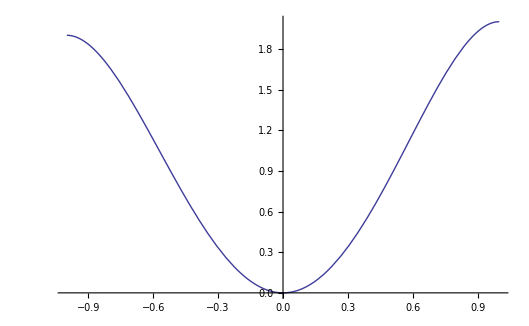

{1/40 (156 Cos[u]^2+5 Cos[u]^3-78 Cos[u]^4-3 Cos[u]^5+40 Cos[v] Sin[u]),Sin[u] Sin[v],Cos[u]}

{1/40 (156 Cos[u]^2+5 Cos[u]^3-78 Cos[u]^4-3 Cos[u]^5+40 Cos[v] Sin[u]),3/10 Sin[u] Sin[v],Cos[u]}

{{Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2,-1/200 Cos[u] Sin[u] (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v]},{-1/200 Cos[u] Sin[u] (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v],9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2}}

{{(9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2)/(-(Cos[u]^2 Sin[u]^2 (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2 Sin[v]^2)/40000+(Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2)),(Cos[u] Sin[u] (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v])/(200 (-(Cos[u]^2 Sin[u]^2 (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2 Sin[v]^2)/40000+(Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2)))},{(Cos[u] Sin[u] (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v])/(200 (-(Cos[u]^2 Sin[u]^2 (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2 Sin[v]^2)/40000+(Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2))),(Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2)/(-(Cos[u]^2 Sin[u]^2 (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2 Sin[v]^2)/40000+(Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2))}}

1/400 Sin[u] √(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))

-Graphics3D-

```mathematica
XG={x[u,v],y[u,v],z[u,v]};
XS={Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]}; 
c=2
r=19/20
XQ=XS+c*Cos[u]^2*{1,1,0};
XO=XS+c*Cos[u]^2*(2-Cos[u]^2)*{1,0,0};
XO2=XS+(c*(Cos[u]^2-1)^2+Cos[u]^2*(2-Cos[u]^2))*{1,0,0};
DWN[z_,C1_,C2_]:=(z^2/4)*(-3*(C1-C2)*z^3-2*(C1+C2)*z^2+5*(C1-C2)*z+4*(C1+C2));
DWN[z,c,r*c]//Simplify
Plot[DWN[z,c,r*c],{z,-1,1}]
XN=XS+DWN[Cos[u],c,r*c]*{1,0,0}//Simplify
(*Manipulate[ParametricPlot3D[(X/.c->cc),{u,0,π},{v,0,2 π}],{cc,0,2}]*)
B=7/10;
(*XNP = XN - B/(1+B)*XS[[2]]*{0,1,0}//Simplify*)
XNP = XN - B*XS[[2]]*{0,1,0};
X= XNP
g=MetricFromPara[X,u,v]//Simplify
gInv=Inverse[g]//Simplify
vol= Sqrt[Det[g]]//Simplify
$Assumptions=0<u&&u<π&&0≤v&&v<2π&&t>0&&v>0&&v<2π;
ParametricPlot3D[X,{u,0,π},{v,0,2π}]
```

```mathematica
Xu=D[X,u]//Simplify
Xv=D[X,v]//Simplify
nuDirection=Cross[Xu,Xv]//Simplify;
nu=(1/Sqrt[nuDirection.nuDirection])*nuDirection//Simplify;
```

{1/40 Cos[u] (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]),3/10 Cos[u] Sin[v],-Sin[u]}

{-Sin[u] Sin[v],3/10 Cos[v] Sin[u],0}

```mathematica
HVec=-Table[LBeltrami0[X[[i]],u,v,g],{i,3}]//Simplify;
H=HVec.nu//Simplify
```

(2400 (15 Cos[u]^4 (8320 Cos[v]-64821 Sin[u]) Sin[u] (Cos[v]^2+Sin[v]^2)+1200 Cos[u]^5 (5 Cos[v]-78 Sin[u]) Sin[u] (Cos[v]^2+Sin[v]^2)+484470 Cos[u]^6 Sin[u]^2 (Cos[v]^2+Sin[v]^2)+46800 Cos[u]^7 Sin[u]^2 (Cos[v]^2+Sin[v]^2)+1125 Cos[u]^8 Sin[u]^2 (Cos[v]^2+Sin[v]^2)-60 Cos[u] Cos[v] Sin[u]^3 (9 Cos[v]^2+100 Sin[v]^2)+120 Cos[u]^3 Sin[u] (390 Cos[v]^2 Sin[u]+Cos[v]^3 (-50+9 Sin[u]^2)+390 Sin[u] Sin[v]^2+50 Cos[v] (-1+2 Sin[u]^2) Sin[v]^2)+16 Cos[u]^2 (545 Cos[v]^4+39 Cos[v]^3 Sin[u] (-200+27 Sin[u]^2)+30420 Sin[u]^2 Sin[v]^2+3900 Cos[v] Sin[u] (-2+3 Sin[u]^2) Sin[v]^2+545 Sin[v]^4+10 Cos[v]^2 (3042 Sin[u]^2+109 Sin[v]^2))+16 Sin[u]^2 (45 Cos[v]^4-351 Cos[v]^3 Sin[u]-3900 Cos[v] Sin[u] Sin[v]^2+Cos[v]^2 (500+545 Sin[v]^2)+500 (Sin[v]^2+Sin[v]^4))))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))^(3/2)

```mathematica
Xuu=D[Xu,u]//Simplify;
Xuv=D[Xu,v]//Simplify;
Xvv=D[Xv,v]//Simplify;
II={{nu.Xuu,nu.Xuv},{nu.Xuv,nu.Xvv}}//Simplify
S=Inverse[g].II//Simplify
K=Det[S]//Simplify
```

{{-(6 (-15 Cos[u] Cos[v] Sin[u]^3+30 Cos[u]^3 Cos[v] Sin[u]^3+4 Sin[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+4 Cos[u]^2 (5 Cos[v]^2+117 Cos[v] Sin[u]^3+5 Sin[v]^2)))/(√(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))),0},{0,-(3 Cos[v]^2 Sin[u]^3)/(10 √(9/100 Cos[v]^2 Sin[u]^4+Sin[u]^4 Sin[v]^2+(9 Cos[u]^2 Sin[u]^2 (40 Cos[v]^2+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Cos[v] Sin[u]+40 Sin[v]^2)^2)/160000))-(3 Sin[u]^3 Sin[v]^2)/(10 √(9/100 Cos[v]^2 Sin[u]^4+Sin[u]^4 Sin[v]^2+(9 Cos[u]^2 Sin[u]^2 (40 Cos[v]^2+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Cos[v] Sin[u]+40 Sin[v]^2)^2)/160000))}}

{{-(9600 (9 Cos[v]^2+100 Sin[v]^2) (-15 Cos[u] Cos[v] Sin[u]^3+30 Cos[u]^3 Cos[v] Sin[u]^3+4 Sin[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+4 Cos[u]^2 (5 Cos[v]^2+117 Cos[v] Sin[u]^3+5 Sin[v]^2)))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))^(3/2),-(96000 Cos[u] Sin[u] (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v] (Cos[v]^2+Sin[v]^2))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))^(3/2)},{-(4800 Cot[u] (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v] (-15 Cos[u] Cos[v] Sin[u]^3+30 Cos[u]^3 Cos[v] Sin[u]^3+4 Sin[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+4 Cos[u]^2 (5 Cos[v]^2+117 Cos[v] Sin[u]^3+5 Sin[v]^2)))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))^(3/2),((Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (-(3 Cos[v]^2 Sin[u]^3)/(10 √(9/100 Cos[v]^2 Sin[u]^4+Sin[u]^4 Sin[v]^2+(9 Cos[u]^2 Sin[u]^2 (40 Cos[v]^2+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Cos[v] Sin[u]+40 Sin[v]^2)^2)/160000))-(3 Sin[u]^3 Sin[v]^2)/(10 √(9/100 Cos[v]^2 Sin[u]^4+Sin[u]^4 Sin[v]^2+(9 Cos[u]^2 Sin[u]^2 (40 Cos[v]^2+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Cos[v] Sin[u]+40 Sin[v]^2)^2)/160000))))/(-(Cos[u]^2 Sin[u]^2 (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2 Sin[v]^2)/40000+(Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2))}}

(115200000 (Cos[v]^2+Sin[v]^2) (-15 Cos[u] Cos[v] Sin[u]^3+30 Cos[u]^3 Cos[v] Sin[u]^3+4 Sin[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+4 Cos[u]^2 (5 Cos[v]^2+117 Cos[v] Sin[u]^3+5 Sin[v]^2)))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))^2

```mathematica
errH=Tr[S]+H//Simplify
errH/.{u->1.3,v->3.7}
```

-(9600 (9 Cos[v]^2+100 Sin[v]^2) (-15 Cos[u] Cos[v] Sin[u]^3+30 Cos[u]^3 Cos[v] Sin[u]^3+4 Sin[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+4 Cos[u]^2 (5 Cos[v]^2+117 Cos[v] Sin[u]^3+5 Sin[v]^2)))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))^(3/2)+((Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (-(3 Cos[v]^2 Sin[u]^3)/(10 √(9/100 Cos[v]^2 Sin[u]^4+Sin[u]^4 Sin[v]^2+(9 Cos[u]^2 Sin[u]^2 (40 Cos[v]^2+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Cos[v] Sin[u]+40 Sin[v]^2)^2)/160000))-(3 Sin[u]^3 Sin[v]^2)/(10 √(9/100 Cos[v]^2 Sin[u]^4+Sin[u]^4 Sin[v]^2+(9 Cos[u]^2 Sin[u]^2 (40 Cos[v]^2+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Cos[v] Sin[u]+40 Sin[v]^2)^2)/160000))))/(-(Cos[u]^2 Sin[u]^2 (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2 Sin[v]^2)/40000+(Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2))+(2400 (15 Cos[u]^4 (8320 Cos[v]-64821 Sin[u]) Sin[u] (Cos[v]^2+Sin[v]^2)+1200 Cos[u]^5 (5 Cos[v]-78 Sin[u]) Sin[u] (Cos[v]^2+Sin[v]^2)+484470 Cos[u]^6 Sin[u]^2 (Cos[v]^2+Sin[v]^2)+46800 Cos[u]^7 Sin[u]^2 (Cos[v]^2+Sin[v]^2)+1125 Cos[u]^8 Sin[u]^2 (Cos[v]^2+Sin[v]^2)-60 Cos[u] Cos[v] Sin[u]^3 (9 Cos[v]^2+100 Sin[v]^2)+120 Cos[u]^3 Sin[u] (390 Cos[v]^2 Sin[u]+Cos[v]^3 (-50+9 Sin[u]^2)+390 Sin[u] Sin[v]^2+50 Cos[v] (-1+2 Sin[u]^2) Sin[v]^2)+16 Cos[u]^2 (545 Cos[v]^4+39 Cos[v]^3 Sin[u] (-200+27 Sin[u]^2)+30420 Sin[u]^2 Sin[v]^2+3900 Cos[v] Sin[u] (-2+3 Sin[u]^2) Sin[v]^2+545 Sin[v]^4+10 Cos[v]^2 (3042 Sin[u]^2+109 Sin[v]^2))+16 Sin[u]^2 (45 Cos[v]^4-351 Cos[v]^3 Sin[u]-3900 Cos[v] Sin[u] Sin[v]^2+Cos[v]^2 (500+545 Sin[v]^2)+500 (Sin[v]^2+Sin[v]^4))))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))^(3/2)

-2.66454×10^-15

```mathematica
subsxyz={Cos[u]->z,Sin[u]->Sqrt[1-z^2],Cos[v]->(x-DWN[z,c,r*c])/Sqrt[1-z^2],Sin[v]->y/(1-B)/Sqrt[1-z^2],Cot[u]->z/Sqrt[1-z^2],Csc[u]->1/Sqrt[1-z^2]}//Simplify
```

{Cos[u]→z,Sin[u]→√(1-z^2),Cos[v]→(40 x+z^2 (-156-5 z+78 z^2+3 z^3))/(40 √(1-z^2)),Sin[v]→(10 y)/(3 √(1-z^2)),Cot[u]→z/(√(1-z^2)),Csc[u]→1/(√(1-z^2))}

```mathematica
DDWN[z_,c1_,c2_]:=(D[DWN[ζ,c1,c2],ζ]//.ζ->z//Simplify)
DDWN[z,c,r*c]
```

-3/40 z (-104-5 z+104 z^2+5 z^3)

```mathematica
(*f=X[[1]]+(X[[1]]+1)^2*(X[[3]]+1)^2/100//Simplify*)
(*f=X[[1]]*X[[2]]//Simplify*)
f=X[[1]]
df=ExD0[f,u,v]//Simplify
gf=Sharp1[df,g]//Simplify
gfGlob=GlobalVecFromPara[gf,X,u,v]//Simplify
gfR3=TrigExpand[gfGlob]//.subsxyz//Simplify
gfR3Para=(gfR3[[1]]*iHat+gfR3[[2]]*jHat+gfR3[[3]]*kHat)/.{x->coordsX,y->coordsY,z->coordsZ}//InputForm
```

1/40 (156 Cos[u]^2+5 Cos[u]^3-78 Cos[u]^4-3 Cos[u]^5+40 Cos[v] Sin[u])

{1/40 Cos[u] (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]),-Sin[u] Sin[v]}

{(360 Cos[u] Cos[v] (40 Cos[v]^2+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Cos[v] Sin[u]+40 Sin[v]^2))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2)),-(40 Csc[u] Sin[v] (-135 Cos[u]^3 Cos[v] Sin[u]+2808 Cos[u]^4 Cos[v] Sin[u]+135 Cos[u]^5 Cos[v] Sin[u]+4000 Sin[u]^2+72 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))}

{(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+160000 Sin[u]^2 Sin[v]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2)),-(48000 Cos[v] Sin[u]^2 Sin[v])/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2)),-(360 Cos[u] Cos[v] Sin[u] (40 Cos[v]^2+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Cos[v] Sin[u]+40 Sin[v]^2))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))}

{((-1+z^2)^2 (14400 x^2 (-160000+876096 z^2+84240 z^3-1750167 z^4-168480 z^5+872046 z^6+84240 z^7+2025 z^8)-160000 y^2 (-160000+876096 z^2+84240 z^3-1750167 z^4-168480 z^5+872046 z^6+84240 z^7+2025 z^8)+720 x z^2 (15974400+368000 z-140165376 z^2-17569920 z^3+340940340 z^4+44232723 z^5-271457082 z^6-35893611 z^7+66777048 z^8+9176733 z^9+410670 z^10+6075 z^11)+9 (256000000+1191833600 z^2+134784000 z^3-5292273600 z^4-429312000 z^5+25205032256 z^6+3749740800 z^7-64725251568 z^8-10470087576 z^9+68664833937 z^10+11429662140 z^11-31278705660 z^12-5379528492 z^13+4990980726 z^14+913115268 z^15+59532084 z^16+1705860 z^17+18225 z^18)))/(2 (207360000 x^4 z^2+25600000000 y^4 z^2-10368000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+14400 x^2 (14400+64 (13239+5000 y^2) z^2+84240 z^3-859671 z^4-126360 z^5-4050 z^6+54756 z^7+441018 z^8+8424 z^9-110322 z^10-4212 z^11+81 z^12)+81 z^4 (156+5 z-78 z^2-3 z^3)^2 (1600+94144 z^2+9360 z^3-290207 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)-320000 y^2 (-80000+160000 z^2-518048 z^4-35100 z^5+875421 z^6+75114 z^7-655542 z^8-57564 z^9+163053 z^10+14742 z^11+324 z^12)+720 x z^2 (-160000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+9 (-249600-8000 z-14561664 z^2-1926080 z^3+44975892 z^4+6235627 z^5-60338226 z^6-8679102 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15)))),-(57600000 y (-1+z^2)^2 (40 x+z^2 (-156-5 z+78 z^2+3 z^3)))/(207360000 x^4 z^2+25600000000 y^4 z^2-10368000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+14400 x^2 (14400+64 (13239+5000 y^2) z^2+84240 z^3-859671 z^4-126360 z^5-4050 z^6+54756 z^7+441018 z^8+8424 z^9-110322 z^10-4212 z^11+81 z^12)+81 z^4 (156+5 z-78 z^2-3 z^3)^2 (1600+94144 z^2+9360 z^3-290207 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)-320000 y^2 (-80000+160000 z^2-518048 z^4-35100 z^5+875421 z^6+75114 z^7-655542 z^8-57564 z^9+163053 z^10+14742 z^11+324 z^12)+720 x z^2 (-160000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+9 (-249600-8000 z-14561664 z^2-1926080 z^3+44975892 z^4+6235627 z^5-60338226 z^6-8679102 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15))),-(540 z (-1+z^2)^2 (14400 x^2 (-104-5 z+104 z^2+5 z^3)-160000 y^2 (-104-5 z+104 z^2+5 z^3)+240 x (1600+48672 z^2+3900 z^3-72933 z^4-6006 z^5+24216 z^6+2106 z^7+45 z^8)+3 (-499200-24000 z+499200 z^2+32000 z^3-7842432 z^4-866160 z^5+15154464 z^6+1751817 z^7-9424740 z^8-1136883 z^9+1853280 z^10+236691 z^11+9828 z^12+135 z^13)))/(207360000 x^4 z^2+25600000000 y^4 z^2-10368000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+14400 x^2 (14400+64 (13239+5000 y^2) z^2+84240 z^3-859671 z^4-126360 z^5-4050 z^6+54756 z^7+441018 z^8+8424 z^9-110322 z^10-4212 z^11+81 z^12)+81 z^4 (156+5 z-78 z^2-3 z^3)^2 (1600+94144 z^2+9360 z^3-290207 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)-320000 y^2 (-80000+160000 z^2-518048 z^4-35100 z^5+875421 z^6+75114 z^7-655542 z^8-57564 z^9+163053 z^10+14742 z^11+324 z^12)+720 x z^2 (-160000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+9 (-249600-8000 z-14561664 z^2-1926080 z^3+44975892 z^4+6235627 z^5-60338226 z^6-8679102 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15)))}

((-1 + coordsZ^2)^2*(14400*coordsX^2*(-160000 + 876096*coordsZ^2 + 84240*coordsZ^3 - 1750167*coordsZ^4 - 168480*coordsZ^5 + 872046*coordsZ^6 + 
      84240*coordsZ^7 + 2025*coordsZ^8) - 160000*coordsY^2*(-160000 + 876096*coordsZ^2 + 84240*coordsZ^3 - 1750167*coordsZ^4 - 
      168480*coordsZ^5 + 872046*coordsZ^6 + 84240*coordsZ^7 + 2025*coordsZ^8) + 
    720*coordsX*coordsZ^2*(15974400 + 368000*coordsZ - 140165376*coordsZ^2 - 17569920*coordsZ^3 + 340940340*coordsZ^4 + 44232723*coordsZ^5 - 
      271457082*coordsZ^6 - 35893611*coordsZ^7 + 66777048*coordsZ^8 + 9176733*coordsZ^9 + 410670*coordsZ^10 + 6075*coordsZ^11) + 
    9*(256000000 + 1191833600*coordsZ^2 + 134784000*coordsZ^3 - 5292273600*coordsZ^4 - 429312000*coordsZ^5 + 25205032256*coordsZ^6 + 
      3749740800*coordsZ^7 - 64725251568*coordsZ^8 - 10470087576*coordsZ^9 + 68664833937*coordsZ^10 + 11429662140*coordsZ^11 - 
      31278705660*coordsZ^12 - 5379528492*coordsZ^13 + 4990980726*coordsZ^14 + 913115268*coordsZ^15 + 59532084*coordsZ^16 + 
      1705860*coordsZ^17 + 18225*coordsZ^18))*iHat)/(2*(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 
    10368000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
    14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 
      54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 
    81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 
      29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
      144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 
      655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 
    720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
      9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 
        8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
        417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15)))) - 
 (57600000*coordsY*(-1 + coordsZ^2)^2*(40*coordsX + coordsZ^2*(-156 - 5*coordsZ + 78*coordsZ^2 + 3*coordsZ^3))*jHat)/
  (207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*
    (312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
   14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 
     54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 
   81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 
     29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
     144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 
     655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 
   720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
     9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 
       8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
       417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))) - 
 (540*coordsZ*(-1 + coordsZ^2)^2*(14400*coordsX^2*(-104 - 5*coordsZ + 104*coordsZ^2 + 5*coordsZ^3) - 
    160000*coordsY^2*(-104 - 5*coordsZ + 104*coordsZ^2 + 5*coordsZ^3) + 
    240*coordsX*(1600 + 48672*coordsZ^2 + 3900*coordsZ^3 - 72933*coordsZ^4 - 6006*coordsZ^5 + 24216*coordsZ^6 + 2106*coordsZ^7 + 
      45*coordsZ^8) + 3*(-499200 - 24000*coordsZ + 499200*coordsZ^2 + 32000*coordsZ^3 - 7842432*coordsZ^4 - 866160*coordsZ^5 + 
      15154464*coordsZ^6 + 1751817*coordsZ^7 - 9424740*coordsZ^8 - 1136883*coordsZ^9 + 1853280*coordsZ^10 + 236691*coordsZ^11 + 
      9828*coordsZ^12 + 135*coordsZ^13))*kHat)/(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 
   10368000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
   14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 
     54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 
   81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 
     29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
     144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 
     655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 
   720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
     9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 
       8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
       417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15)))

```mathematica
StringReplace[ToString[gfR3Para],{"Sqrt"->"sqrt","["->"(","]"->")"}]//FullForm
```

"((-1 + coordsZ^2)^2*(14400*coordsX^2*(-160000 + 876096*coordsZ^2 + 84240*coordsZ^3 - 1750167*coordsZ^4 - 168480*coordsZ^5 + 872046*coordsZ^6 + 84240*coordsZ^7 + 2025*coordsZ^8) - 160000*coordsY^2*(-160000 + 876096*coordsZ^2 + 84240*coordsZ^3 - 1750167*coordsZ^4 - 168480*coordsZ^5 + 872046*coordsZ^6 + 84240*coordsZ^7 + 2025*coordsZ^8) + 720*coordsX*coordsZ^2*(15974400 + 368000*coordsZ - 140165376*coordsZ^2 - 17569920*coordsZ^3 + 340940340*coordsZ^4 + 44232723*coordsZ^5 - 271457082*coordsZ^6 - 35893611*coordsZ^7 + 66777048*coordsZ^8 + 9176733*coordsZ^9 + 410670*coordsZ^10 + 6075*coordsZ^11) + 9*(256000000 + 1191833600*coordsZ^2 + 134784000*coordsZ^3 - 5292273600*coordsZ^4 - 429312000*coordsZ^5 + 25205032256*coordsZ^6 + 3749740800*coordsZ^7 - 64725251568*coordsZ^8 - 10470087576*coordsZ^9 + 68664833937*coordsZ^10 + 11429662140*coordsZ^11 - 31278705660*coordsZ^12 - 5379528492*coordsZ^13 + 4990980726*coordsZ^14 + 913115268*coordsZ^15 + 59532084*coordsZ^16 + 1705860*coordsZ^17 + 18225*coordsZ^18))*iHat)/(2*(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15)))) - (57600000*coordsY*(-1 + coordsZ^2)^2*(40*coordsX + coordsZ^2*(-156 - 5*coordsZ + 78*coordsZ^2 + 3*coordsZ^3))*jHat)/(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))) - (540*coordsZ*(-1 + coordsZ^2)^2*(14400*coordsX^2*(-104 - 5*coordsZ + 104*coordsZ^2 + 5*coordsZ^3) - 160000*coordsY^2*(-104 - 5*coordsZ + 104*coordsZ^2 + 5*coordsZ^3) + 240*coordsX*(1600 + 48672*coordsZ^2 + 3900*coordsZ^3 - 72933*coordsZ^4 - 6006*coordsZ^5 + 24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8) + 3*(-499200 - 24000*coordsZ + 499200*coordsZ^2 + 32000*coordsZ^3 - 7842432*coordsZ^4 - 866160*coordsZ^5 + 15154464*coordsZ^6 + 1751817*coordsZ^7 - 9424740*coordsZ^8 - 1136883*coordsZ^9 + 1853280*coordsZ^10 + 236691*coordsZ^11 + 9828*coordsZ^12 + 135*coordsZ^13))*kHat)/(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15)))"

```mathematica
StringReplace[ToString[(f/.subsxyz//Simplify)/.{x->coordsX,y->coordsY,z->coordsZ}//InputForm],{"Sqrt"->"sqrt","["->"(","]"->")"}]//FullForm
```

"(100*coordsY^2)/9 - (coordsZ^2*(312 - 40*coordsX + 15*coordsZ - 468*coordsZ^2 - 25*coordsZ^3 + 234*coordsZ^4 + 12*coordsZ^5)^2)/(1600*(-1 + coordsZ^2))"

```mathematica
w={0,1}
wGlob=GlobalVecFromPara[w,X,u,v]//Simplify
wR3=TrigExpand[wGlob]//.subsxyz//Simplify
wR3Para=(wR3[[1]]*iHat+wR3[[2]]*jHat+wR3[[3]]*kHat)/.{x->coordsX,y->coordsY,z->coordsZ}//InputForm
```

{0,1}

{-Sin[u] Sin[v],3/10 Cos[v] Sin[u],0}

{-(10 y)/3,3/400 (40 x+z^2 (-156-5 z+78 z^2+3 z^3)),0}

(-10*coordsY*iHat)/3 + (3*(40*coordsX + coordsZ^2*(-156 - 5*coordsZ + 78*coordsZ^2 + 3*coordsZ^3))*jHat)/400

```mathematica
StringReplace[ToString[wR3Para],{"Sqrt"->"sqrt","["->"(","]"->")","Pi"->ToString[π//N]}]//FullForm
```

"(-10*coordsY*iHat)/3 + (3*(40*coordsX + coordsZ^2*(-156 - 5*coordsZ + 78*coordsZ^2 + 3*coordsZ^3))*jHat)/400"

```mathematica
vecGlobGen=RotationMatrix[1/20,{-1,0,1}].{0,1,0}
vec=LocalVecFromPara[vecGlobGen,X,u,v]//Simplify
vecGlob=GlobalVecFromPara[vec,X,u,v]//Simplify
vecR3=TrigExpand[vecGlob]//.subsxyz//Simplify
vecR3Para=(vecR3[[1]]*iHat+vecR3[[2]]*jHat+vecR3[[3]]*kHat)/.{x->coordsX,y->coordsY,z->coordsZ}//InputForm
```

{-Sin[1/20]/(√2),Cos[1/20],-Sin[1/20]/(√2)}

{-(20 (-45 Cos[u]^2 Cos[v] Sin[u] (3 √2 Cos[v] Sin[1/20]-20 Cos[1/20] Sin[v])+936 Cos[u]^3 Cos[v] Sin[u] (3 √2 Cos[v] Sin[1/20]-20 Cos[1/20] Sin[v])+45 Cos[u]^4 Cos[v] Sin[u] (3 √2 Cos[v] Sin[1/20]-20 Cos[1/20] Sin[v])+24 Cos[u] (3 √2 Cos[v] Sin[1/20]-20 Cos[1/20] Sin[v]) (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-40 √2 Sin[1/20] Sin[u] (9 Cos[v]^2+100 Sin[v]^2)))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2)),(Sin[u] (Cos[u] (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]) Sin[v] ((Sin[1/20] Sin[u])/(√2)-(Cos[u] Sin[1/20] (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u]))/(40 √2)+3/10 Cos[1/20] Cos[u] Sin[v])+20 (3 Cos[1/20] Cos[v]+5 √2 Sin[1/20] Sin[v]) (Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2)))/(200 (-(Cos[u]^2 Sin[u]^2 (182 Cos[v]+15 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2 Sin[v]^2)/40000+(Sin[u]^2+(Cos[u]^2 (40 Cos[v]+3 (-104-5 Cos[u]+104 Cos[u]^2+5 Cos[u]^3) Sin[u])^2)/1600+9/100 Cos[u]^2 Sin[v]^2) (9/100 Cos[v]^2 Sin[u]^2+Sin[u]^2 Sin[v]^2)))}

{-(872046 √2 Cos[u]^6 Cos[v]^2 Sin[1/20] Sin[u]^2+84240 √2 Cos[u]^7 Cos[v]^2 Sin[1/20] Sin[u]^2+2025 √2 Cos[u]^8 Cos[v]^2 Sin[1/20] Sin[u]^2+32000 Sin[u]^2 Sin[v] (3 Cos[1/20] Cos[v]+5 √2 Sin[1/20] Sin[v])+2160 √2 Cos[u]^5 Cos[v] Sin[1/20] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2880 √2 Cos[u] Cos[v] Sin[1/20] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-2160 √2 Cos[u]^3 Cos[v] Sin[1/20] Sin[u] (5 Cos[v]^2+13 Cos[v] Sin[u]+5 Sin[v]^2)+27 √2 Cos[u]^4 Cos[v] Sin[1/20] Sin[u] (8320 Cos[v]^2-65021 Cos[v] Sin[u]+8320 Sin[v]^2)+72 √2 Cos[u]^2 Sin[1/20] (200 Cos[v]^4-3120 Cos[v]^3 Sin[u]-3120 Cos[v] Sin[u] Sin[v]^2+200 Sin[v]^4+Cos[v]^2 (12243 Sin[u]^2+400 Sin[v]^2)))/(2 (872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))),(3 (290682 Cos[1/20] Cos[u]^6 Cos[v]^2 Sin[u]^2+28080 Cos[1/20] Cos[u]^7 Cos[v]^2 Sin[u]^2+675 Cos[1/20] Cos[u]^8 Cos[v]^2 Sin[u]^2+1600 Cos[v] Sin[u]^2 (3 Cos[1/20] Cos[v]+5 √2 Sin[1/20] Sin[v])+720 Cos[1/20] Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)+1600 √2 Cos[u] Sin[1/20] Sin[u] Sin[v] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-240 Cos[u]^3 Cos[v] Sin[u] (15 Cos[1/20] Cos[v]^2-117 Cos[1/20] Cos[v] Sin[u]+5 Sin[v] (-52 √2 Sin[1/20] Sin[u]+3 Cos[1/20] Sin[v]))+3 Cos[u]^4 Cos[v] Sin[u] (24960 Cos[1/20] Cos[v]^2-194463 Cos[1/20] Cos[v] Sin[u]+40 Sin[v] (25 √2 Sin[1/20] Sin[u]+624 Cos[1/20] Sin[v]))+24 Cos[u]^2 (200 Cos[1/20] Cos[v]^4-3120 Cos[1/20] Cos[v]^3 Sin[u]+200 Cos[1/20] Sin[v]^4-5 Cos[v] Sin[u] Sin[v] (25 √2 Sin[1/20] Sin[u]+624 Cos[1/20] Sin[v])+8 Cos[1/20] Cos[v]^2 (1521 Sin[u]^2+50 Sin[v]^2))))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2)),(20 Sin[u] (-45 Cos[u]^2 Cos[v] Sin[u] (3 √2 Cos[v] Sin[1/20]-20 Cos[1/20] Sin[v])+936 Cos[u]^3 Cos[v] Sin[u] (3 √2 Cos[v] Sin[1/20]-20 Cos[1/20] Sin[v])+45 Cos[u]^4 Cos[v] Sin[u] (3 √2 Cos[v] Sin[1/20]-20 Cos[1/20] Sin[v])+24 Cos[u] (3 √2 Cos[v] Sin[1/20]-20 Cos[1/20] Sin[v]) (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)-40 √2 Sin[1/20] Sin[u] (9 Cos[v]^2+100 Sin[v]^2)))/(872046 Cos[u]^6 Cos[v]^2 Sin[u]^2+84240 Cos[u]^7 Cos[v]^2 Sin[u]^2+2025 Cos[u]^8 Cos[v]^2 Sin[u]^2+2160 Cos[u]^5 Cos[v] Sin[u] (5 Cos[v]^2-78 Cos[v] Sin[u]+5 Sin[v]^2)-2160 Cos[u]^3 Cos[v] Sin[u] (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)+576 Cos[u]^2 (5 Cos[v]^2-39 Cos[v] Sin[u]+5 Sin[v]^2)^2+1600 Sin[u]^2 (9 Cos[v]^2+100 Sin[v]^2)+27 Cos[u]^4 Cos[v] Sin[u] (8320 Cos[v]^2-64821 Cos[v] Sin[u]+8320 Sin[v]^2))}

{-((-1+z^2)^2 (230400000 y z^2 (-156-5 z+78 z^2+3 z^3) Cos[1/20]+14400 √2 x^2 (-160000+112320 z+881496 z^2-28080 z^3-1755567 z^4-168480 z^5+872046 z^6+84240 z^7+2025 z^8) Sin[1/20]-160000 √2 y^2 (-160000+112320 z+881496 z^2-28080 z^3-1755567 z^4-168480 z^5+872046 z^6+84240 z^7+2025 z^8) Sin[1/20]+9 √2 (256000000+179712000 z+1200473600 z^2-44928000 z^3-5303793600 z^4+2393963520 z^5+25516849856 z^6-1705866240 z^7-65355905688 z^8-7077181176 z^9+69074111817 z^10+10762481340 z^11-31363914420 z^12-5383066572 z^13+4990932126 z^14+913115268 z^15+59532084 z^16+1705860 z^17+18225 z^18) Sin[1/20]+720 x (12800000 y Cos[1/20]+√2 z (-576000+15974400 z-17153920 z^2-141569376 z^3+8685960 z^4+343102500 z^5+35514963 z^6-272215242 z^7-35909811 z^8+66777048 z^9+9176733 z^10+410670 z^11+6075 z^12) Sin[1/20])))/(4 (207360000 x^4 z^2+25600000000 y^4 z^2-10368000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+14400 x^2 (14400+64 (13239+5000 y^2) z^2+84240 z^3-859671 z^4-126360 z^5-4050 z^6+54756 z^7+441018 z^8+8424 z^9-110322 z^10-4212 z^11+81 z^12)+81 z^4 (156+5 z-78 z^2-3 z^3)^2 (1600+94144 z^2+9360 z^3-290207 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)-320000 y^2 (-80000+160000 z^2-518048 z^4-35100 z^5+875421 z^6+75114 z^7-655542 z^8-57564 z^9+163053 z^10+14742 z^11+324 z^12)+720 x z^2 (-160000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+9 (-249600-8000 z-14561664 z^2-1926080 z^3+44975892 z^4+6235627 z^5-60338226 z^6-8679102 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15)))),(9 (-1+z^2)^2 (14400 x^2 (1600+97344 z^2+9360 z^3-194463 z^4-18720 z^5+96894 z^6+9360 z^7+225 z^8) Cos[1/20]-160000 y^2 (1600+97344 z^2+9360 z^3-194463 z^4-18720 z^5+96894 z^6+9360 z^7+225 z^8) Cos[1/20]+9 (2560000+158310400 z^2+14976000 z^3-116452800 z^4-17472000 z^5+2329465984 z^6+383385600 z^7-7074381552 z^8-1154274264 z^9+7629600393 z^10+1269962460 z^11-3475411740 z^12-597725388 z^13+554553414 z^14+101457252 z^15+6614676 z^16+189540 z^17+2025 z^18) Cos[1/20]+160000 √2 y z (1600-6240 z+48472 z^2+7020 z^3-72813 z^4-6006 z^5+24216 z^6+2106 z^7+45 z^8) Sin[1/20]+80 x (-17046720 z^5 Cos[1/20]+340940340 z^6 Cos[1/20]+44232723 z^7 Cos[1/20]-271457082 z^8 Cos[1/20]-35893611 z^9 Cos[1/20]+66777048 z^10 Cos[1/20]+9176733 z^11 Cos[1/20]+410670 z^12 Cos[1/20]+6075 z^13 Cos[1/20]+3200000 √2 y Sin[1/20]-24960000 √2 y z Sin[1/20]-384 z^4 (329589 Cos[1/20]-3125 √2 y Sin[1/20])-24000 z^3 (21 Cos[1/20]-1040 √2 y Sin[1/20])-48000 z^2 (234 Cos[1/20]+25 √2 y Sin[1/20]))))/(2 (207360000 x^4 z^2+25600000000 y^4 z^2-10368000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+14400 x^2 (14400+64 (13239+5000 y^2) z^2+84240 z^3-859671 z^4-126360 z^5-4050 z^6+54756 z^7+441018 z^8+8424 z^9-110322 z^10-4212 z^11+81 z^12)+81 z^4 (156+5 z-78 z^2-3 z^3)^2 (1600+94144 z^2+9360 z^3-290207 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)-320000 y^2 (-80000+160000 z^2-518048 z^4-35100 z^5+875421 z^6+75114 z^7-655542 z^8-57564 z^9+163053 z^10+14742 z^11+324 z^12)+720 x z^2 (-160000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+9 (-249600-8000 z-14561664 z^2-1926080 z^3+44975892 z^4+6235627 z^5-60338226 z^6-8679102 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15)))),(10 (-1+z^2)^2 (-144000 y z (1600+48672 z^2+3900 z^3-72933 z^4-6006 z^5+24216 z^6+2106 z^7+45 z^8+120 x (-104-5 z+104 z^2+5 z^3)) Cos[1/20]-160000 √2 y^2 (3640-2808 z-135 z^2+2808 z^3+135 z^4) Sin[1/20]+9 √2 (-6976000-4492800 z+6760000 z^2+4492800 z^3+88871040 z^4-64903488 z^5-96287480 z^6+130143936 z^7+37802913 z^8-83119140 z^9-10199187 z^10+16679520 z^11+2130219 z^12+88452 z^13+1215 z^14+1600 x^2 (3640-2808 z-135 z^2+2808 z^3+135 z^4)+80 x z (14400-567840 z+419848 z^2+319020 z^3-645477 z^4-54054 z^5+217944 z^6+18954 z^7+405 z^8)) Sin[1/20]))/(207360000 x^4 z^2+25600000000 y^4 z^2-10368000 x^3 z^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+14400 x^2 (14400+64 (13239+5000 y^2) z^2+84240 z^3-859671 z^4-126360 z^5-4050 z^6+54756 z^7+441018 z^8+8424 z^9-110322 z^10-4212 z^11+81 z^12)+81 z^4 (156+5 z-78 z^2-3 z^3)^2 (1600+94144 z^2+9360 z^3-290207 z^4-29640 z^5+364290 z^6+37908 z^7-218039 z^8-22932 z^9+54156 z^10+5616 z^11+144 z^12)-320000 y^2 (-80000+160000 z^2-518048 z^4-35100 z^5+875421 z^6+75114 z^7-655542 z^8-57564 z^9+163053 z^10+14742 z^11+324 z^12)+720 x z^2 (-160000 y^2 (312+15 z-312 z^2-20 z^3+156 z^4+9 z^5)+9 (-249600-8000 z-14561664 z^2-1926080 z^3+44975892 z^4+6235627 z^5-60338226 z^6-8679102 z^7+43253964 z^8+6412520 z^9-16776396 z^10-2526174 z^11+2724696 z^12+417861 z^13+20358 z^14+324 z^15)))}

(10*(-1 + coordsZ^2)^2*kHat*(-144000*coordsY*coordsZ*(1600 + 48672*coordsZ^2 + 3900*coordsZ^3 - 72933*coordsZ^4 - 6006*coordsZ^5 + 
      24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8 + 120*coordsX*(-104 - 5*coordsZ + 104*coordsZ^2 + 5*coordsZ^3))*Cos[1/20] - 
    160000*Sqrt[2]*coordsY^2*(3640 - 2808*coordsZ - 135*coordsZ^2 + 2808*coordsZ^3 + 135*coordsZ^4)*Sin[1/20] + 
    9*Sqrt[2]*(-6976000 - 4492800*coordsZ + 6760000*coordsZ^2 + 4492800*coordsZ^3 + 88871040*coordsZ^4 - 64903488*coordsZ^5 - 
      96287480*coordsZ^6 + 130143936*coordsZ^7 + 37802913*coordsZ^8 - 83119140*coordsZ^9 - 10199187*coordsZ^10 + 16679520*coordsZ^11 + 
      2130219*coordsZ^12 + 88452*coordsZ^13 + 1215*coordsZ^14 + 1600*coordsX^2*(3640 - 2808*coordsZ - 135*coordsZ^2 + 2808*coordsZ^3 + 
        135*coordsZ^4) + 80*coordsX*coordsZ*(14400 - 567840*coordsZ + 419848*coordsZ^2 + 319020*coordsZ^3 - 645477*coordsZ^4 - 
        54054*coordsZ^5 + 217944*coordsZ^6 + 18954*coordsZ^7 + 405*coordsZ^8))*Sin[1/20]))/
  (207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*
    (312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
   14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 
     54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 
   81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 
     29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
     144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 
     655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 
   720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
     9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 
       8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
       417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))) - 
 ((-1 + coordsZ^2)^2*iHat*(230400000*coordsY*coordsZ^2*(-156 - 5*coordsZ + 78*coordsZ^2 + 3*coordsZ^3)*Cos[1/20] + 
    14400*Sqrt[2]*coordsX^2*(-160000 + 112320*coordsZ + 881496*coordsZ^2 - 28080*coordsZ^3 - 1755567*coordsZ^4 - 168480*coordsZ^5 + 
      872046*coordsZ^6 + 84240*coordsZ^7 + 2025*coordsZ^8)*Sin[1/20] - 160000*Sqrt[2]*coordsY^2*
     (-160000 + 112320*coordsZ + 881496*coordsZ^2 - 28080*coordsZ^3 - 1755567*coordsZ^4 - 168480*coordsZ^5 + 872046*coordsZ^6 + 
      84240*coordsZ^7 + 2025*coordsZ^8)*Sin[1/20] + 9*Sqrt[2]*(256000000 + 179712000*coordsZ + 1200473600*coordsZ^2 - 44928000*coordsZ^3 - 
      5303793600*coordsZ^4 + 2393963520*coordsZ^5 + 25516849856*coordsZ^6 - 1705866240*coordsZ^7 - 65355905688*coordsZ^8 - 
      7077181176*coordsZ^9 + 69074111817*coordsZ^10 + 10762481340*coordsZ^11 - 31363914420*coordsZ^12 - 5383066572*coordsZ^13 + 
      4990932126*coordsZ^14 + 913115268*coordsZ^15 + 59532084*coordsZ^16 + 1705860*coordsZ^17 + 18225*coordsZ^18)*Sin[1/20] + 
    720*coordsX*(12800000*coordsY*Cos[1/20] + Sqrt[2]*coordsZ*(-576000 + 15974400*coordsZ - 17153920*coordsZ^2 - 141569376*coordsZ^3 + 
        8685960*coordsZ^4 + 343102500*coordsZ^5 + 35514963*coordsZ^6 - 272215242*coordsZ^7 - 35909811*coordsZ^8 + 66777048*coordsZ^9 + 
        9176733*coordsZ^10 + 410670*coordsZ^11 + 6075*coordsZ^12)*Sin[1/20])))/
  (4*(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*
     (312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
    14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 
      54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 
    81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 
      29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
      144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 
      655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 
    720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
      9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 
        8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
        417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15)))) + 
 (9*(-1 + coordsZ^2)^2*jHat*(14400*coordsX^2*(1600 + 97344*coordsZ^2 + 9360*coordsZ^3 - 194463*coordsZ^4 - 18720*coordsZ^5 + 96894*coordsZ^6 + 
      9360*coordsZ^7 + 225*coordsZ^8)*Cos[1/20] - 160000*coordsY^2*(1600 + 97344*coordsZ^2 + 9360*coordsZ^3 - 194463*coordsZ^4 - 
      18720*coordsZ^5 + 96894*coordsZ^6 + 9360*coordsZ^7 + 225*coordsZ^8)*Cos[1/20] + 
    9*(2560000 + 158310400*coordsZ^2 + 14976000*coordsZ^3 - 116452800*coordsZ^4 - 17472000*coordsZ^5 + 2329465984*coordsZ^6 + 
      383385600*coordsZ^7 - 7074381552*coordsZ^8 - 1154274264*coordsZ^9 + 7629600393*coordsZ^10 + 1269962460*coordsZ^11 - 
      3475411740*coordsZ^12 - 597725388*coordsZ^13 + 554553414*coordsZ^14 + 101457252*coordsZ^15 + 6614676*coordsZ^16 + 189540*coordsZ^17 + 
      2025*coordsZ^18)*Cos[1/20] + 160000*Sqrt[2]*coordsY*coordsZ*(1600 - 6240*coordsZ + 48472*coordsZ^2 + 7020*coordsZ^3 - 72813*coordsZ^4 - 
      6006*coordsZ^5 + 24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8)*Sin[1/20] + 
    80*coordsX*(-17046720*coordsZ^5*Cos[1/20] + 340940340*coordsZ^6*Cos[1/20] + 44232723*coordsZ^7*Cos[1/20] - 271457082*coordsZ^8*Cos[1/20] - 
      35893611*coordsZ^9*Cos[1/20] + 66777048*coordsZ^10*Cos[1/20] + 9176733*coordsZ^11*Cos[1/20] + 410670*coordsZ^12*Cos[1/20] + 
      6075*coordsZ^13*Cos[1/20] + 3200000*Sqrt[2]*coordsY*Sin[1/20] - 24960000*Sqrt[2]*coordsY*coordsZ*Sin[1/20] - 
      384*coordsZ^4*(329589*Cos[1/20] - 3125*Sqrt[2]*coordsY*Sin[1/20]) - 24000*coordsZ^3*(21*Cos[1/20] - 1040*Sqrt[2]*coordsY*Sin[1/20]) - 
      48000*coordsZ^2*(234*Cos[1/20] + 25*Sqrt[2]*coordsY*Sin[1/20]))))/
  (2*(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*
     (312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
    14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 
      54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 
    81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 
      29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 
      144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 
      655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 
    720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 
      9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 
        8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 
        417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))))

```mathematica
StringReplace[ToString[vecR3Para],{"Sqrt"->"sqrt","Cos"->"cos","Sin"->"sin","["->"(","]"->")","Pi"->ToString[π//N]}]//FullForm
```

"(10*(-1 + coordsZ^2)^2*kHat*(-144000*coordsY*coordsZ*(1600 + 48672*coordsZ^2 + 3900*coordsZ^3 - 72933*coordsZ^4 - 6006*coordsZ^5 + 24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8 + 120*coordsX*(-104 - 5*coordsZ + 104*coordsZ^2 + 5*coordsZ^3))*cos(1/20) - 160000*sqrt(2)*coordsY^2*(3640 - 2808*coordsZ - 135*coordsZ^2 + 2808*coordsZ^3 + 135*coordsZ^4)*sin(1/20) + 9*sqrt(2)*(-6976000 - 4492800*coordsZ + 6760000*coordsZ^2 + 4492800*coordsZ^3 + 88871040*coordsZ^4 - 64903488*coordsZ^5 - 96287480*coordsZ^6 + 130143936*coordsZ^7 + 37802913*coordsZ^8 - 83119140*coordsZ^9 - 10199187*coordsZ^10 + 16679520*coordsZ^11 + 2130219*coordsZ^12 + 88452*coordsZ^13 + 1215*coordsZ^14 + 1600*coordsX^2*(3640 - 2808*coordsZ - 135*coordsZ^2 + 2808*coordsZ^3 + 135*coordsZ^4) + 80*coordsX*coordsZ*(14400 - 567840*coordsZ + 419848*coordsZ^2 + 319020*coordsZ^3 - 645477*coordsZ^4 - 54054*coordsZ^5 + 217944*coordsZ^6 + 18954*coordsZ^7 + 405*coordsZ^8))*sin(1/20)))/(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))) - ((-1 + coordsZ^2)^2*iHat*(230400000*coordsY*coordsZ^2*(-156 - 5*coordsZ + 78*coordsZ^2 + 3*coordsZ^3)*cos(1/20) + 14400*sqrt(2)*coordsX^2*(-160000 + 112320*coordsZ + 881496*coordsZ^2 - 28080*coordsZ^3 - 1755567*coordsZ^4 - 168480*coordsZ^5 + 872046*coordsZ^6 + 84240*coordsZ^7 + 2025*coordsZ^8)*sin(1/20) - 160000*sqrt(2)*coordsY^2*(-160000 + 112320*coordsZ + 881496*coordsZ^2 - 28080*coordsZ^3 - 1755567*coordsZ^4 - 168480*coordsZ^5 + 872046*coordsZ^6 + 84240*coordsZ^7 + 2025*coordsZ^8)*sin(1/20) + 9*sqrt(2)*(256000000 + 179712000*coordsZ + 1200473600*coordsZ^2 - 44928000*coordsZ^3 - 5303793600*coordsZ^4 + 2393963520*coordsZ^5 + 25516849856*coordsZ^6 - 1705866240*coordsZ^7 - 65355905688*coordsZ^8 - 7077181176*coordsZ^9 + 69074111817*coordsZ^10 + 10762481340*coordsZ^11 - 31363914420*coordsZ^12 - 5383066572*coordsZ^13 + 4990932126*coordsZ^14 + 913115268*coordsZ^15 + 59532084*coordsZ^16 + 1705860*coordsZ^17 + 18225*coordsZ^18)*sin(1/20) + 720*coordsX*(12800000*coordsY*cos(1/20) + sqrt(2)*coordsZ*(-576000 + 15974400*coordsZ - 17153920*coordsZ^2 - 141569376*coordsZ^3 + 8685960*coordsZ^4 + 343102500*coordsZ^5 + 35514963*coordsZ^6 - 272215242*coordsZ^7 - 35909811*coordsZ^8 + 66777048*coordsZ^9 + 9176733*coordsZ^10 + 410670*coordsZ^11 + 6075*coordsZ^12)*sin(1/20))))/(4*(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15)))) + (9*(-1 + coordsZ^2)^2*jHat*(14400*coordsX^2*(1600 + 97344*coordsZ^2 + 9360*coordsZ^3 - 194463*coordsZ^4 - 18720*coordsZ^5 + 96894*coordsZ^6 + 9360*coordsZ^7 + 225*coordsZ^8)*cos(1/20) - 160000*coordsY^2*(1600 + 97344*coordsZ^2 + 9360*coordsZ^3 - 194463*coordsZ^4 - 18720*coordsZ^5 + 96894*coordsZ^6 + 9360*coordsZ^7 + 225*coordsZ^8)*cos(1/20) + 9*(2560000 + 158310400*coordsZ^2 + 14976000*coordsZ^3 - 116452800*coordsZ^4 - 17472000*coordsZ^5 + 2329465984*coordsZ^6 + 383385600*coordsZ^7 - 7074381552*coordsZ^8 - 1154274264*coordsZ^9 + 7629600393*coordsZ^10 + 1269962460*coordsZ^11 - 3475411740*coordsZ^12 - 597725388*coordsZ^13 + 554553414*coordsZ^14 + 101457252*coordsZ^15 + 6614676*coordsZ^16 + 189540*coordsZ^17 + 2025*coordsZ^18)*cos(1/20) + 160000*sqrt(2)*coordsY*coordsZ*(1600 - 6240*coordsZ + 48472*coordsZ^2 + 7020*coordsZ^3 - 72813*coordsZ^4 - 6006*coordsZ^5 + 24216*coordsZ^6 + 2106*coordsZ^7 + 45*coordsZ^8)*sin(1/20) + 80*coordsX*(-17046720*coordsZ^5*cos(1/20) + 340940340*coordsZ^6*cos(1/20) + 44232723*coordsZ^7*cos(1/20) - 271457082*coordsZ^8*cos(1/20) - 35893611*coordsZ^9*cos(1/20) + 66777048*coordsZ^10*cos(1/20) + 9176733*coordsZ^11*cos(1/20) + 410670*coordsZ^12*cos(1/20) + 6075*coordsZ^13*cos(1/20) + 3200000*sqrt(2)*coordsY*sin(1/20) - 24960000*sqrt(2)*coordsY*coordsZ*sin(1/20) - 384*coordsZ^4*(329589*cos(1/20) - 3125*sqrt(2)*coordsY*sin(1/20)) - 24000*coordsZ^3*(21*cos(1/20) - 1040*sqrt(2)*coordsY*sin(1/20)) - 48000*coordsZ^2*(234*cos(1/20) + 25*sqrt(2)*coordsY*sin(1/20)))))/(2*(207360000*coordsX^4*coordsZ^2 + 25600000000*coordsY^4*coordsZ^2 - 10368000*coordsX^3*coordsZ^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 14400*coordsX^2*(14400 + 64*(13239 + 5000*coordsY^2)*coordsZ^2 + 84240*coordsZ^3 - 859671*coordsZ^4 - 126360*coordsZ^5 - 4050*coordsZ^6 + 54756*coordsZ^7 + 441018*coordsZ^8 + 8424*coordsZ^9 - 110322*coordsZ^10 - 4212*coordsZ^11 + 81*coordsZ^12) + 81*coordsZ^4*(156 + 5*coordsZ - 78*coordsZ^2 - 3*coordsZ^3)^2*(1600 + 94144*coordsZ^2 + 9360*coordsZ^3 - 290207*coordsZ^4 - 29640*coordsZ^5 + 364290*coordsZ^6 + 37908*coordsZ^7 - 218039*coordsZ^8 - 22932*coordsZ^9 + 54156*coordsZ^10 + 5616*coordsZ^11 + 144*coordsZ^12) - 320000*coordsY^2*(-80000 + 160000*coordsZ^2 - 518048*coordsZ^4 - 35100*coordsZ^5 + 875421*coordsZ^6 + 75114*coordsZ^7 - 655542*coordsZ^8 - 57564*coordsZ^9 + 163053*coordsZ^10 + 14742*coordsZ^11 + 324*coordsZ^12) + 720*coordsX*coordsZ^2*(-160000*coordsY^2*(312 + 15*coordsZ - 312*coordsZ^2 - 20*coordsZ^3 + 156*coordsZ^4 + 9*coordsZ^5) + 9*(-249600 - 8000*coordsZ - 14561664*coordsZ^2 - 1926080*coordsZ^3 + 44975892*coordsZ^4 + 6235627*coordsZ^5 - 60338226*coordsZ^6 - 8679102*coordsZ^7 + 43253964*coordsZ^8 + 6412520*coordsZ^9 - 16776396*coordsZ^10 - 2526174*coordsZ^11 + 2724696*coordsZ^12 + 417861*coordsZ^13 + 20358*coordsZ^14 + 324*coordsZ^15))))"

```mathematica
RotationMatrix[phi,{-1,0,1}].{0,1,0}
```

{-Sin[phi]/(√2),Cos[phi],-Sin[phi]/(√2)}